```mathematica
D2a[n_,k_]:=D2a[n,k]=Sum[D2a[Floor[n/j],k-1],{j,2,n}];D2a[n_,0]:=1
DD[n_,z_]:=DD[n,z]=Sum[FactorialPower[z,a]/a! D2a[n,a],{a,0,Log[2,n]}]
d[n_,z_]:=Product[(-1)^p[[2]] Binomial[-z,p[[2]]],{p,FI[n]}];FI[n_]:=FactorInteger[n];FI[1]:={}
ReferernceD[n_,z_]:=Sum[d[j,z],{j,1,n}]
E2a[n_,k_, a_]:= E2a[n,k,a]=Sum[ E2a[n/j,k-1,a],{j,2,n}]-a Sum[ E2a[n/(a j),k-1,a],{j,1,n/a}];E2a[n_,0,a_]:=1
EE[n_,z_,b_]:=EE[n,z,b]=Sum[FactorialPower[z,a]/a! E2a[n,a,b],{a,0,Log[If[b>2,2,b],n]}]
EAlt[ n_, z_, b_] := Sum[ (-1)^j Binomial[z,j] b^j ReferernceD[ n/(b^j), z],{j,0, Log[b,n]}]
DAlt[ n_, z_, b_] := Sum[ (-1)^j Binomial[-z,j] b^j EE[ n/(b^j), z, b],{j,0, Log[b,n]}]
Enull[ n_, z_, b_] := Sum[ (-1)^j Binomial[z,j] b^j Dnull[ n/(b^j), z],{j,0, Log[b,n]}]
Dnll[ n_, z_, b_] := Sum[ (-1)^j Binomial[-z,j] b^j Enll[ n/(b^j), z, b],{j,0, Log[b,n]}]
```

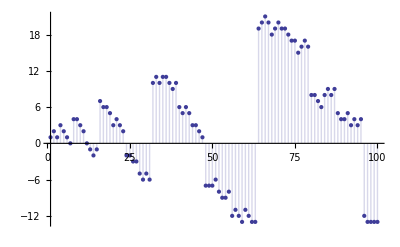

```mathematica
DiscretePlot[ EE[n,-1,2],{n,1,100}]
```

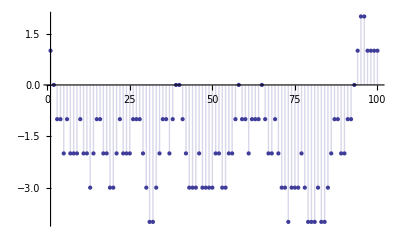

```mathematica
DiscretePlot[DAlt[n,-1,3],{n,1,100}]
```

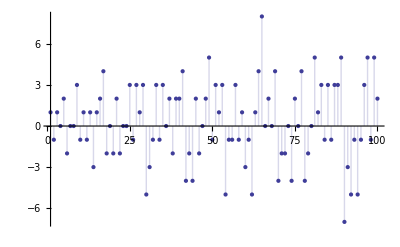

```mathematica
DiscretePlot[ EAlt[n,2,2],{n,1,100}]
```

```mathematica
Enull[ 100, 2, 2]
```

4 Dnull[25,2]-4 Dnull[50,2]+Dnull[100,2]

```mathematica
Dnll[ 100, -1, 2]
```

-2 Enll[50,-1,2]+Enll[100,-1,2]